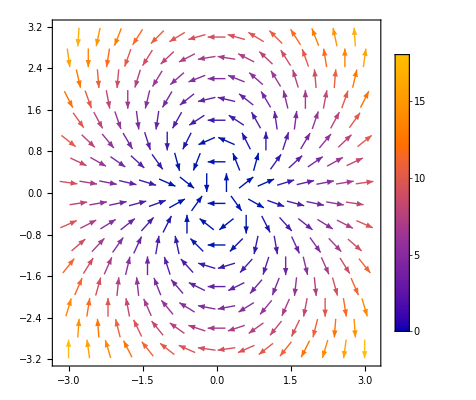

```mathematica
ComplexVectorPlot[z^2,{z,-3-3I,3+3I},PlotLegends->Automatic]
```

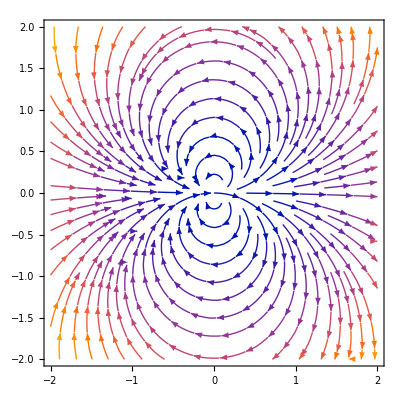

```mathematica
ComplexStreamPlot[z^2,{z,-2-2I,2+2I}]
```

```mathematica
grid =Join@@Table[{x,y},{x,-3,3},{y,-3,3}]
```

{{-3,-3},{-3,-2},{-3,-1},{-3,0},{-3,1},{-3,2},{-3,3},{-2,-3},{-2,-2},{-2,-1},{-2,0},{-2,1},{-2,2},{-2,3},{-1,-3},{-1,-2},{-1,-1},{-1,0},{-1,1},{-1,2},{-1,3},{0,-3},{0,-2},{0,-1},{0,0},{0,1},{0,2},{0,3},{1,-3},{1,-2},{1,-1},{1,0},{1,1},{1,2},{1,3},{2,-3},{2,-2},{2,-1},{2,0},{2,1},{2,2},{2,3},{3,-3},{3,-2},{3,-1},{3,0},{3,1},{3,2},{3,3}}

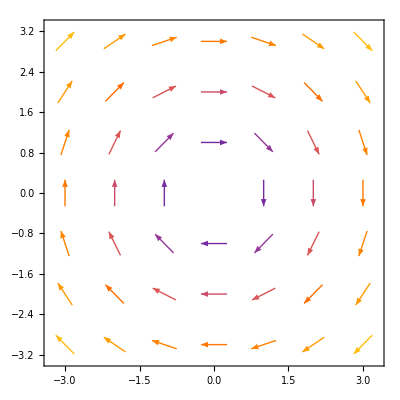

```mathematica
VectorPlot[{y,-x},{x,-3,3},{y,-3,3},VectorPoints->grid]
```

```mathematica
points=RandomReal[{-3,3},{20,2}];
```

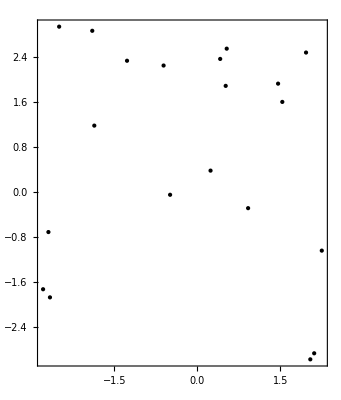

```mathematica
Graphics[{PointSize[Large],Point[points]},Frame->True]
```

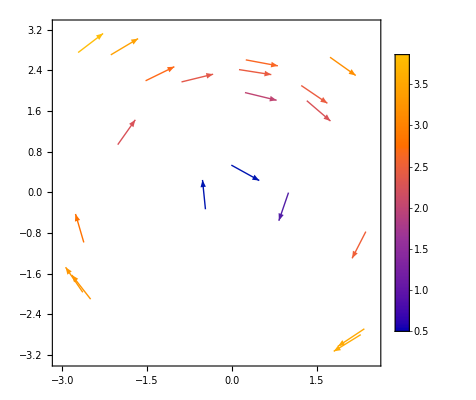

```mathematica
VectorPlot[{y,-x},{x,-3,3},{y,-3,3},VectorPoints->points,PlotLegends->Automatic]
```

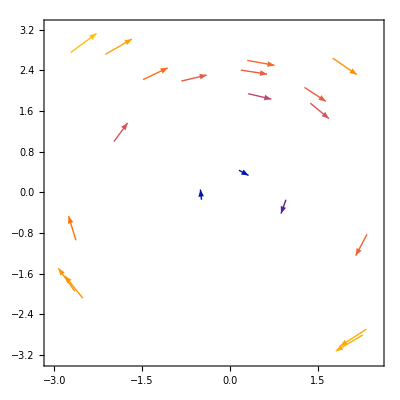

```mathematica
VectorPlot[{y,-x},{x,-3,3},{y,-3,3},VectorPoints->points,VectorScaling->Automatic]
```

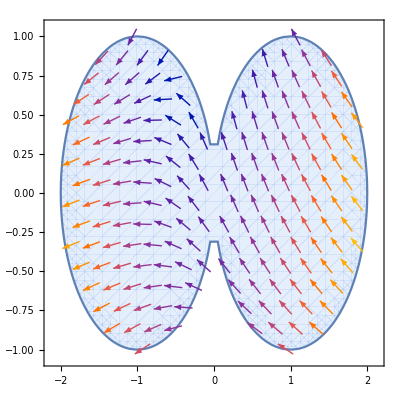

```mathematica
VectorPlot[{-1-x^2+y,1+x-y^2},{x,y}∈RegionUnion[Disk[{-1,0}],Disk[{1,0}]]]
```

```mathematica
SliceVectorPlot3D[{x,y,z},"CenterCutSphere",{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

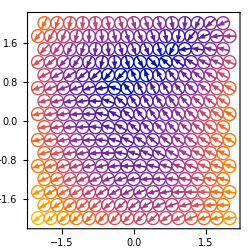

```mathematica
VectorPlot[{-1-x^2+y,1+x-y^2},{x,-2,2},{y,-2,2},
VectorPoints->"Hexagonal",
VectorMarkers->"CircleArrow",
VectorSizes->1,
ImageSize->250]
```

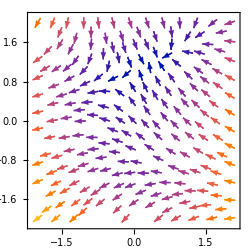
{-Graphics-,-Graphics3D-}

```mathematica
{VectorPlot[{-1-x^2+y,1+x-y^2},{x,-2,2},{y,-2,2},VectorPoints->"Mesh",VectorMarkers->"Arrow",ImageSize->250],Plot3D[Norm[{-1-x^2+y,1+x-y^2}],{x,-2,2},{y,-2,2},Mesh->All,ImageSize->250]}
```

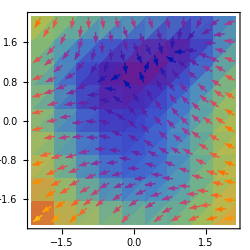

```mathematica
VectorDensityPlot[
{-1-x^2+y,1+x-y^2},{x,-2,2},{y,-2,2},
VectorPoints->"Mesh",
ImageSize->250,
ColorFunction->"Rainbow"
]
```

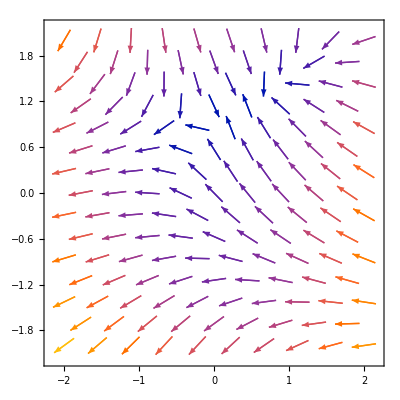

```mathematica
VectorPlot[
{-1-x^2+y,1+x-y^2},{x,-2,2},{y,-2,2},
VectorPoints->{"Hexagonal",10,15},
VectorMarkers->"Arrow"
]
```

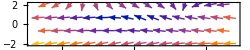
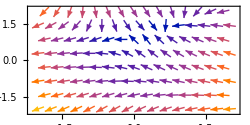
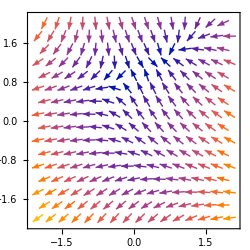
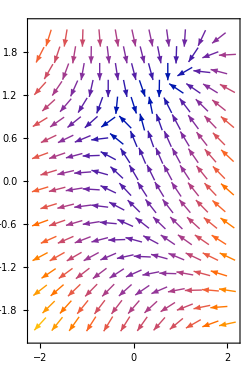

```mathematica
Table[VectorPlot[
{-1-x^2+y,1+x-y^2},{x,-2,2},{y,-2,2},
VectorPoints->Automatic,
ImageSize->250,
AspectRatio->ar,
VectorSizes->1
],{ar,{0.2,0.5,1,1.5}}]
```

```mathematica
{VectorPlot3D[
{-1-x^2+y,1+x-y^2,z},{x,-2,2},{y,-2,2},{z,-2,2},
VectorPoints->"Hexagonal",
ImageSize->400
],
VectorPlot3D[
{-1-x^2+y,1+x-y^2,z},{x,-2,2},{y,-2,2},{z,-2,2},
VectorPoints->"FaceCenteredCubic",
ImageSize->400
]
}
```

{-Graphics3D-,-Graphics3D-}

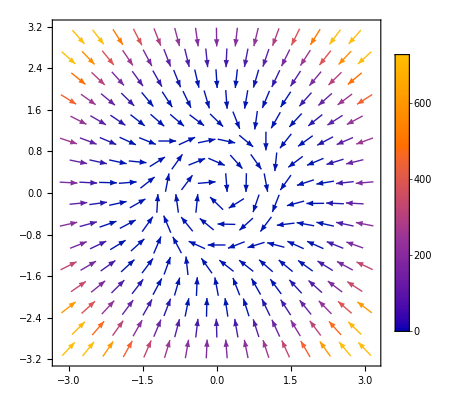

```mathematica
VectorPlot[{y-x (1-x^2-y^2)^2,-x-y (1-x^2-y^2)^2},{x,-3,3},{y,-3,3},PlotLegends->Automatic]
```

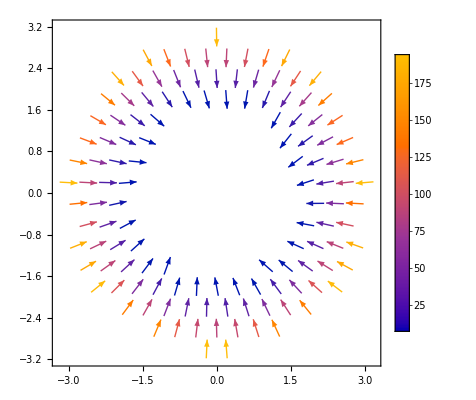

```mathematica
VectorPlot[{y-x (1-x^2-y^2)^2,-x-y (1-x^2-y^2)^2},{x,-3,3},{y,-3,3},PlotLegends->Automatic,
VectorRange->{5,200},
ClippingStyle->None
]
```

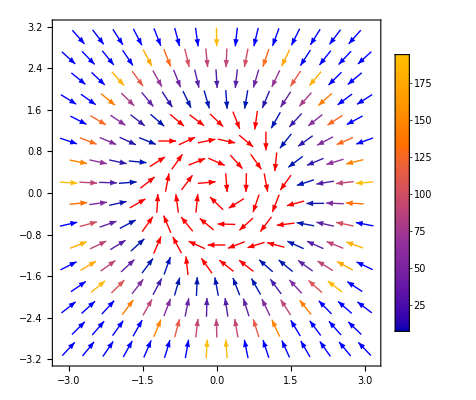

```mathematica
VectorPlot[{y-x (1-x^2-y^2)^2,-x-y (1-x^2-y^2)^2},{x,-3,3},{y,-3,3},PlotLegends->Automatic,
VectorRange->{5,200},
ClippingStyle->{Red,Blue}
]
```

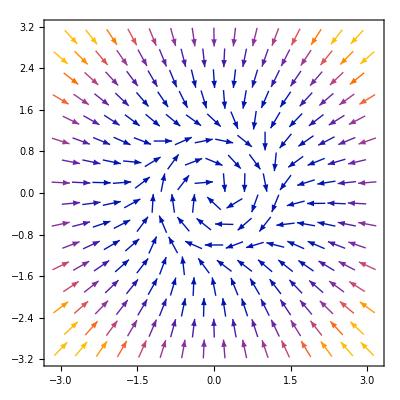
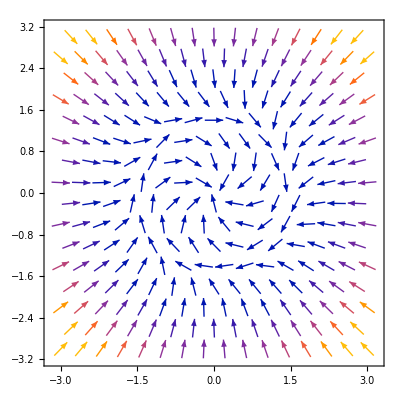
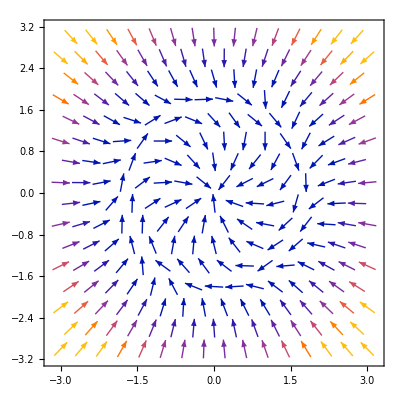

```mathematica
{VectorPlot[{y-x (1-x^2-y^2)^2,-x-y (1-x^2-y^2)^2},{x,-3,3},{y,-3,3}
],
VectorPlot[{y-x (2-x^2-y^2)^2,-x-y (2-x^2-y^2)^2},{x,-3,3},{y,-3,3}
],
VectorPlot[{y-x (3-x^2-y^2)^2,-x-y (3-x^2-y^2)^2},{x,-3,3},{y,-3,3}
]}
```